10

0.250769

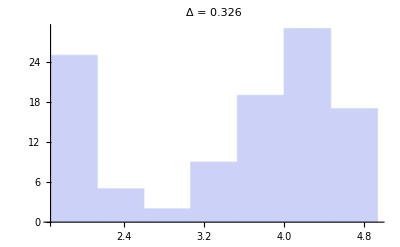
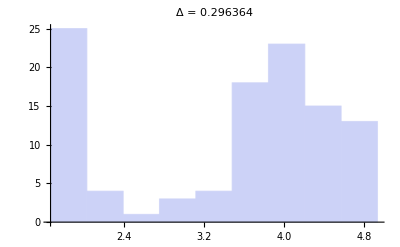
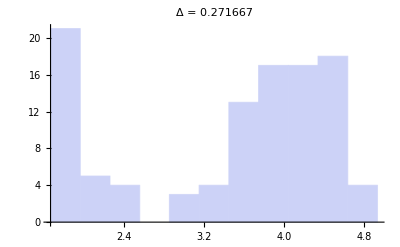
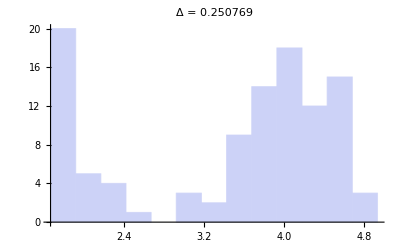
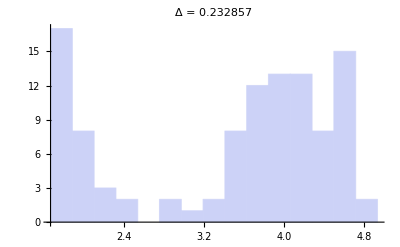
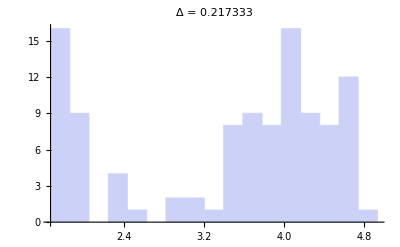
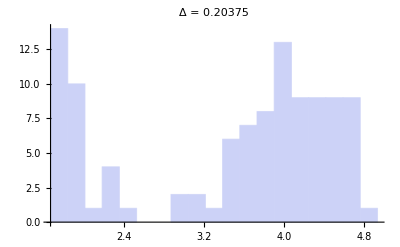

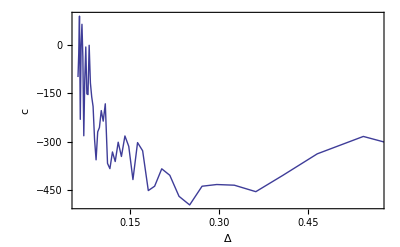

```mathematica
(*2006 Author Hideaki Shimazaki Department of Physics, Kyoto University 
shimazaki at ton.scphys.kyoto-u.ac.jp 
Please feel free to use/modify/distribute this program.*)
(*Data:the duration for eruptions of the Old Faithful geyser in Yellowstone National Park (in minutes)*)
x={4.37,3.87,4.00 ,4.03, 3.50, 4.08, 2.25, 4.70, 1.73, 4.93, 1.73, 4.62, 3.43, 4.25, 1.68, 3.92, 3.68, 3.10, 4.03, 1.77, 4.08, 1.75, 3.20, 1.85,4.62, 1.97, 4.50, 3.92, 4.35, 2.33, 3.83 ,1.88, 4.60, 1.80, 4.73, 1.77, 4.57, 1.85, 3.52, 4.00, 3.70, 3.72, 4.25, 3.58, 3.80, 3.77, 3.75, 2.50,4.50, 4.10, 3.70, 3.80, 3.43, 4.00, 2.27, 4.40, 4.05, 4.25, 3.33, 2.00, 4.33, 2.93, 4.58, 1.90, 3.58, 3.73, 3.73, 1.82, 4.63, 3.50, 4.00, 3.67, 1.67, 4.60, 1.67, 4.00, 1.80, 4.42, 1.90 ,4.63, 2.93, 3.50, 1.97, 4.28, 1.83, 4.13, 1.83, 4.65, 4.20, 3.93, 4.33, 1.83, 4.53, 2.03, 4.18, 4.43, 4.07, 4.13, 3.95, 4.10, 2.27, 4.58, 1.90, 4.50, 1.95, 4.83, 4.12};
d={};c={}; p={};Δ={};
For[i=1,i<50,i++,
n=i+3; (* number of bin *)
Δ=Append[Δ,(Max[x]-Min[x])/n]; (* *)
ki=BinCounts[x,{Min[x],Max[x],Δ[[i]]}];
(*Cost Function*)
k = Mean[ki];
v = Variance[ki];
c=Append[c,(2k-v)/Δ[[i]]^2];
p=Append[p,{Δ[[i]],c[[i]]}];
]
(*Optimal Bin Size Selection*)
idx=Ordering[c][[1]]
dopt=Δ[[idx]]
edges={};
edges=Do[Append[edges,Min[x]+dopt*i],{i,0,idx+3}];
(*Display an Optimized Histogram*)
Table[Histogram[x,{Min[x],Max[x],Δ[[idx+2i]]},PlotLabel->"Δ = "<>ToString[Δ[[idx+i]]]],{i,-3,3}]
ListPlot[p,Joined->True,Frame->True, FrameLabel-> {"Δ", "c"}]
```